## myPackage

```mathematica
(*erstellt am 2025-05-03*)
CloudGet[
 CloudObject[
  "https://www.wolframcloud.com/obj/firlecarl/myPackageWL.wl"]]
  
myFontSize=13
myFontStandard="Lucida Sans Unicode"

myStyle["Wolfram Mathematica Version 14.2",22,Background->Yellow]
(*myColorFavorits = TableForm[Table[ColorData[i],{i,{3,24,35,61,97,106,114}}]]
Table[ContourPlot[x+Sin[x^2+y^2],{x,-4,4},{y,-4,4},Contours->9,ContourShading->ColorData[i,"ColorList"]],{i,{3,24,35,61,97,106,114}}]

myColorGradientFavorits=Table[DensityPlot[y+Sin[x^2+3y],{x,-3,3},{y,-3,3},ColorFunction->ColorData[i]],{i,{"RedBlueTones","Rainbow","DarkRainbow","DarkBands","BrightBands","CMYKColors","Pastel","GrayTones"}}]

Table[ColorData[i,"Image"],{i,{"DarkRainbow","Pastel"}}]*)

myColors=ColorData[61]
myColorForGradient=ColorData["DarkRainbow"]
myCMYKColors[]
myBAUAColors[4]

myExportFigureList={};
myExportEquationList={};

impPath = Directory[] ~~ "\\Desktop\\Mathematica\\Quelle\\" (*Import-Pfad anpassen*)
exPath = Directory[] ~~ "\\Desktop\\Mathematica\\Ausgabe\\" (*Export-Pfad anpassen*)

pathSaveVersions = 
 Directory[] ~~ "\\Desktop\\Mathematica\\Versionsverlauf\\" (*Pfad für Versionsverlauf*)
NotebookOpen[
 CloudObject[
  "https://www.wolframcloud.com/obj/firlecarl/Versionsverlauf.nb"]]

myPackageInputPrint[]
```

13

Lucida Sans Unicode

Wolfram Mathematica Version 14.2

ColorDataFunction[…]

ColorDataFunction[…]

{CMYKColor[{0, 0, 1, 0}],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[0, 0.09, 1, 0.03],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}],CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}],CMYKColor[{0, 1, 0, 0}],CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}]}

{RGBColor[0.10196078431372549, 0.4392156862745098, 0.7215686274509804],RGBColor[0.38823529411764707, 0.38823529411764707, 0.3843137254901961],RGBColor[0.9568627450980393, 0.9529411764705882, 0.9254901960784314],RGBColor[0.8901960784313725, 0.8980392156862745, 0.8588235294117647],RGBColor[0.6705882352941176, 0.8196078431372549, 0.5607843137254902],RGBColor[0.4588235294117647, 0.7450980392156863, 0.9176470588235294],RGBColor[0.9254901960784314, 0.4, 0.09019607843137255],RGBColor[0.9450980392156862, 0.7019607843137254, 0.],RGBColor[0.6705882352941176, 0.8196078431372549, 0.5607843137254902],RGBColor[0.06666666666666667, 0.3058823529411765, 0.5058823529411764],RGBColor[0.00392156862745098, 0.3607843137254902, 0.5764705882352941],RGBColor[0.6509803921568628, 0.8196078431372549, 0.9450980392156862],RGBColor[0.8117647058823529, 0.8980392156862745, 0.9725490196078431]}

C:\Users\mona_\Desktop\Mathematica\Quelle\

C:\Users\mona_\Desktop\Mathematica\Ausgabe\

C:\Users\mona_\Desktop\Mathematica\Versionsverlauf\

myAroundString[l_List/;Dimensions[l]⟦2⟧==2]:=Module[{},(StringJoin[ToString[#1⟦1⟧]~~ ± ~~ToString[#1⟦-1⟧]]&)/@l]
myBAUAColors[a_Integer:5]:=Module[{bauaMainColors,bauaHighlightColors,bauaBlueColors,bauaAllColors,bauaDesignColors,bauaCMYKColors},{bauaMainColors→{RGBColor[#1A70B8],RGBColor[#636362],RGBColor[#F4F3EC],RGBColor[#E3E5DB],RGBColor[#ABD18F]},bauaHighlightColors→{RGBColor[#EC6617],RGBColor[#75BEEA],RGBColor[#ABD18F],RGBColor[#F1B300]},bauaBlueColors→{{RGBColor[#114e81],RGBColor[#015c93],RGBColor[#1770b8],RGBColor[#74bdea],RGBColor[#a6d1f1],RGBColor[#cfe5f8]}},bauaAllColors→{RGBColor[#1A70B8],RGBColor[#636362],RGBColor[#F4F3EC],RGBColor[#E3E5DB],RGBColor[#ABD18F],RGBColor[#75BEEA],RGBColor[#EC6617],RGBColor[#F1B300],RGBColor[#ABD18F],RGBColor[#114e81],RGBColor[#015c93],RGBColor[#a6d1f1],RGBColor[#cfe5f8]},bauaDesignColors→{RGBColor[0.4588235294117647, 0.7450980392156863, 0.9176470588235294],RGBColor[0.9254901960784314, 0.4, 0.09019607843137255],RGBColor[0.6705882352941176, 0.8196078431372549, 0.5607843137254902],RGBColor[0.9450980392156862, 0.7019607843137254, 0.],RGBColor[0.10196078431372549, 0.4392156862745098, 0.7215686274509804],RGBColor[0.38823529411764707, 0.38823529411764707, 0.3843137254901961],RGBColor[0.8901960784313725, 0.8980392156862745, 0.8588235294117647],RGBColor[0.8117647058823529, 0.8980392156862745, 0.9725490196078431],RGBColor[0.06666666666666667, 0.3058823529411765, 0.5058823529411764]},bauaCMYKColors→{CMYKColor[0.85, 0.5, 0, 0],CMYKColor[0.85, 0.5, 0, 0, 0.7],CMYKColor[0.85, 0.5, 0, 0, 0.4],CMYKColor[0.85, 0.45, 0, 0.3],CMYKColor[0.85, 0.5, 0, 0.4],CMYKColor[0.85, 0.45, 0, 0.3, 0.7],CMYKColor[0.85, 0.45, 0, 0.3, 0.5],CMYKColor[0.85, 0.45, 0, 0.3, 0.3],CMYKColor[0., 0., 0, 0.75],CMYKColor[0., 0., 0.05, 0.06],CMYKColor[0.08, 0.03, 0.12, 0.07],CMYKColor[0.62, 0.27, 0.92, 0.7],CMYKColor[0.55, 0.1, 0, 0],CMYKColor[0., 0.75, 1, 0],CMYKColor[0., 0.3, 1, 0.05],CMYKColor[0.4, 0., 0.55, 0]}}⟦a,2⟧]
myCMYKColors[a_Integer:1]:=Module[{},{{CMYKColor[{0, 0, 1, 0}],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[0, 0.09, 1, 0.03],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}],CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}],CMYKColor[{0, 1, 0, 0}],CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}]},{Leuchtgelb→CMYKColor[{0, 0, 1, 0}],Zitronengelb→CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],Orange→CMYKColor[{0, Rational[11, 20], 1, 0}],Hellrosa→CMYKColor[{Rational[1, 20], Rational[2, 5], Rational[1, 5], 0}],Altrosa→CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],Feuerrot→CMYKColor[{0, 1, 1, Rational[1, 5]}],Signalrot→CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],Korallenrot→CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],Leuchtrot→CMYKColor[{0, Rational[9, 10], 1, 0}],Reines Rot→CMYKColor[{0, 1, Rational[9, 10], 0}],Weinrot→CMYKColor[{Rational[7, 20], 1, Rational[13, 20], 0}],Pink→CMYKColor[{0, 1, 0, 0}],Lila→CMYKColor[{Rational[1, 2], Rational[3, 5], 0, 0}],Violett→CMYKColor[{Rational[3, 5], Rational[9, 10], 0, Rational[1, 10]}],Azurblau→CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],Himmelblau→CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],Reines Blau→CMYKColor[{1, Rational[7, 10], 0, 0}],Nachtblau→CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],Pastelltürkis→CMYKColor[{Rational[3, 5], Rational[1, 10], Rational[1, 2], 0}],Minttürkis→CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],Türkis→CMYKColor[{Rational[9, 10], Rational[1, 10], Rational[2, 5], Rational[1, 10]}],Leuchtgrün/Gelbgrün→CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],Grün→CMYKColor[{Rational[9, 10], 0, Rational[4, 5], 0}],Grasgrün→CMYKColor[{Rational[9, 10], Rational[1, 5], 1, Rational[1, 4]}],Maigrün→CMYKColor[{Rational[4, 5], Rational[1, 5], 1, Rational[1, 10]}],Rotbraun→CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],Kastanienbraun→CMYKColor[{0, Rational[3, 5], Rational[3, 5], Rational[7, 10]}],Schokobraun→CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],Cremeweiß→CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],Beige→CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],Silbergrau→CMYKColor[{Rational[1, 10], 0, 0, Rational[2, 5]}],Steingrau→CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],Tiefschwarz→CMYKColor[{Rational[2, 5], Rational[1, 5], Rational[1, 5], 1}]},{Leuchtgelb→{CMYKColor[{0, 0, 1, 0}]},Zitronengelb→{CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}]},Orange→{CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{0, Rational[1, 2], 1, 0}],CMYKColor[{0, Rational[11, 20], 1, 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{0, Rational[13, 20], 1, 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}]},Hellrosa→{CMYKColor[{Rational[1, 20], Rational[2, 5], Rational[1, 5], 0}],CMYKColor[{0, Rational[1, 2], Rational[1, 5], Rational[1, 10]}]},Altrosa→{CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[7, 10], Rational[3, 10], Rational[1, 10]}],CMYKColor[{0, Rational[13, 20], Rational[2, 5], Rational[1, 10]}]},Feuerrot→{CMYKColor[{0, 1, 1, Rational[1, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}]},Signalrot→{CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[1, 5], 1, Rational[9, 10], Rational[1, 10]}]},Korallenrot→{CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[3, 10]}]},Leuchtrot→{CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[{0, 1, 1, 0}]},Reines Rot→{CMYKColor[{0, 1, Rational[9, 10], 0}],CMYKColor[{0, 1, Rational[7, 10], 0}]},Weinrot→{CMYKColor[{Rational[1, 5], 1, Rational[4, 5], Rational[2, 5]}],CMYKColor[{Rational[2, 5], 1, Rational[3, 5], Rational[2, 5]}],CMYKColor[{Rational[7, 20], 1, Rational[13, 20], 0}],CMYKColor[{Rational[3, 5], 1, Rational[4, 5], 0}]},Pink→{CMYKColor[{0, 1, 0, 0}]},Lila→{CMYKColor[{Rational[1, 2], Rational[3, 5], 0, 0}],CMYKColor[{Rational[3, 5], Rational[7, 10], Rational[1, 20], Rational[1, 10]}]},Violett→{CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, Rational[1, 10]}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{Rational[9, 10], 1, 0, 0}]},Azurblau→{CMYKColor[{Rational[9, 10], Rational[3, 10], Rational[1, 10], Rational[2, 5]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, Rational[3, 10]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}]},Himmelblau→{CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[9, 10], Rational[1, 2], 0, 0}],CMYKColor[{1, Rational[3, 10], 0, Rational[1, 10]}],CMYKColor[{1, Rational[2, 5], 0, 0}]},Reines Blau→{CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{1, Rational[7, 10], 0, 0}],CMYKColor[{1, Rational[4, 5], 0, 0}],CMYKColor[{Rational[19, 20], Rational[3, 5], 0, Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, Rational[2, 5]}]},Nachtblau→{CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{1, 1, Rational[2, 5], Rational[2, 5]}]},Pastelltürkis→{CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[3, 5], Rational[1, 10], Rational[1, 2], 0}],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], Rational[1, 5]}]},Minttürkis→{CMYKColor[{Rational[4, 5], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{Rational[7, 10], Rational[3, 20], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}]},Türkis→{CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[7, 20], Rational[1, 5]}],CMYKColor[{Rational[9, 10], Rational[1, 10], Rational[2, 5], Rational[1, 10]}]},Leuchtgrün/Gelbgrün→{CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{Rational[3, 5], 0, Rational[19, 20], 0}],CMYKColor[{Rational[7, 10], 0, Rational[9, 10], 0}]},Grün→{CMYKColor[{Rational[13, 20], 0, Rational[4, 5], 0}],CMYKColor[{Rational[9, 10], 0, Rational[4, 5], 0}],CMYKColor[{Rational[17, 20], 0, 1, 0}],CMYKColor[{Rational[17, 20], 0, 1, Rational[1, 10]}]},Grasgrün→{CMYKColor[{Rational[3, 5], 0, Rational[9, 10], Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[21, 25], 0, 1, 0}],CMYKColor[{Rational[9, 10], Rational[1, 5], 1, Rational[1, 4]}],CMYKColor[{Rational[7, 10], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}]},Maigrün→{CMYKColor[{Rational[4, 5], Rational[1, 5], 1, Rational[1, 10]}]},Rotbraun→{CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[1, 20], 1, 1, Rational[4, 5]}]},Kastanienbraun→{CMYKColor[{0, Rational[3, 5], Rational[3, 5], Rational[7, 10]}],CMYKColor[{Rational[1, 2], 1, 1, Rational[1, 2]}],CMYKColor[{0, Rational[9, 10], 1, Rational[4, 5]}]},Schokobraun→{CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{0, Rational[3, 5], Rational[9, 10], Rational[4, 5]}],CMYKColor[{Rational[2, 5], Rational[7, 10], Rational[3, 5], Rational[4, 5]}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{Rational[3, 5], Rational[4, 5], Rational[4, 5], Rational[4, 5]}]},Cremeweiß→{CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}]},Beige→{CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}]},Silbergrau→{CMYKColor[{Rational[1, 10], 0, 0, Rational[2, 5]}]},Steingrau→{CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}]},Tiefschwarz→{CMYKColor[{1, Rational[2, 5], Rational[2, 5], Rational[9, 10]}],CMYKColor[{Rational[2, 5], Rational[1, 5], Rational[1, 5], 1}],CMYKColor[{Rational[3, 10], 0, 0, 1}],CMYKColor[{0, Rational[1, 2], Rational[1, 5], 1}]}}}⟦a⟧]
myExportEquations[l_List]:=Module[{id,eq},((id=#1⟦2⟧;eq=#1⟦1⟧;Export[exPath~~\equations\~~id~~.txt,ExportString[eq,{MathML,Expression}]];If[MemberQ[myExportEquationList⟦All,1⟧,id],myExportEquationList=ReplacePart[myExportEquationList,FirstPosition[myExportEquationList⟦All,1⟧,id]⟦1⟧→{id,eq}];,AppendTo[myExportEquationList,{id,eq}]];)&)/@l Export[exPath~~\equations\##1 equation IDs and equations.pdf,Column[(Row[Riffle[{#1⟦1⟧,#1⟦2⟧},	]]&)/@myExportEquationList]];Export[exPath~~\equations\##2 equation IDs.rtf,StringRiffle[Prepend[myExportEquationList⟦All,1⟧,exPath~~\equations\],
]];]
myExportF[l_List]:=Module[{r,g,nameID,name,icon},((g=#1⟦1⟧;nameID=#1⟦2⟧;name=#1⟦3⟧;If[#1⟦5⟧==True,r=600;Table[Export[exPath~~CMYK ~~ToString[r]~~ dpi\~~nameID~~ _ ~~ToString[r]~~ dpi CMYK~~i,ColorConvert[Rasterize[g,ImageResolution→r],CMYK]],{i,{.eps,.png}}],Nothing];r=72;icon=Rasterize[g,ImageResolution→r];Table[Export[exPath~~ToString[i]~~ ~~ToString[r]~~ dpi\~~nameID~~ _ ~~ToString[r]~~ dpi~~i,icon],{i,{.png}}];r=150;Table[Export[exPath~~ToString[i]~~ ~~ToString[r]~~ dpi\~~nameID~~ _ ~~ToString[r]~~ dpi~~i,Rasterize[g,ImageResolution→r]],{i,{.png}}];r=#1⟦4⟧;Table[Export[exPath~~ToString[i]~~ ~~ToString[r]~~ dpi\~~nameID~~ _ ~~ToString[r]~~ dpi~~i,Rasterize[g,ImageResolution→r]],{i,{.png}}];(Table[Export[exPath~~ToString[i]~~\~~nameID~~i,g],{i,{.svg,.eps,.pdf}}]&)/@#1;If[MemberQ[myExportFigureList⟦All,1⟧,nameID],myExportFigureList=ReplacePart[myExportFigureList,FirstPosition[myExportFigureList⟦All,1⟧,nameID]⟦1⟧→{nameID,name,icon}];,AppendTo[myExportFigureList,{nameID,name,icon}]];)&)/@l;Export[exPath~~##1 full names of figure IDs.pdf,Column[Join[{		ID figure name,		_________},(Row[Riffle[{#1⟦1⟧,#1⟦2⟧,#1⟦3⟧},	]]&)/@myExportFigureList]]];Export[exPath~~##2 figure IDs.rtf,StringRiffle[myExportFigureList⟦All,1⟧,
]];]
myExportFPNG[l_List]:=Module[{r,g,name},((g=#1⟦1⟧;name=#1⟦2⟧;r=#1⟦3⟧;Table[Export[exPath~~name~~ ~~ToString[r]~~ dpi~~i,Rasterize[g,ImageResolution→r]],{i,{.png}}])&)/@l]
myExportFSVG[l_List]:=Module[{r,g,name},((g=#1⟦1⟧;name=#1⟦2⟧;(Table[Export[exPath~~name~~i,g],{i,{.svg}}]&)/@#1)&)/@l]
myFlatten[l_List,level_Integer]:=Module[{},Map[Flatten[#1]&,l,{level}]]
myFrameStyle[fontsize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},FrameStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myFrameTickStyle[fontsize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},FrameTicksStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myLabelStyle[fontsize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},LabelStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myLegendAppearance[markersize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},LegendAppearance→{LegendMarkerSize→markersize,FontFamily→fontfamily,color}]
myPackageInputPrint[]:=Module[{l},l=ToExpression/@(Select[Names[Global`*],StringContainsQ[my~~__]]/.{myExportFunctionList→Nothing,myExportFigureList→Nothing,myExportEquationList→Nothing,myFontSize→Nothing,myFontStandard→Nothing,myColors→Nothing,myFigureIDs→Nothing,myColorForGradient→Nothing,myPlotColors→Nothing});TableForm[Definition/@l]]
myPlotStyle[opacity_:1,colorList_List:myPlotColors]:=Module[{},PlotStyle→(Directive[Opacity[opacity],#1]&)/@colorList]
myReplaceList[lTarget_List,fReplace_]:=Module[{},(#1→fReplace&)/@lTarget]
myStringJoin[l_List,deli_String:,start_Integer:2,end_Integer:-2,step_Integer:2]:=Module[{},StringJoin[Riffle[ToString/@l,deli,{start,end,step}]]]
myStringSplit[s_String,deli_List]:=Module[{i,out,j},i=1;out=StringSplit[s,deli⟦i⟧];For[j=1,j<Length[deli],j++,i++;out=Map[StringSplit[#1,deli⟦i⟧]&,out,{i-1}]];out]
myStyle[s_,fontsize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},Style[If[StringQ[s],s,ToString[s]],FontSize→fontsize,FontFamily→fontfamily,color]]
mySubJoin[lTarget_List,lInsert_List,pos_Integer:1]:=Module[{},(Insert[lTarget⟦#1⟦2⟧⟧,#1⟦1⟧,pos]&)/@lInsert]
myT[l1_List,l2_List]:=Module[{},Transpose[{l1,l2}]]
myTake[lData_List,lSort_List]:=Module[{outList,dimensionQ},If[Length[Dimensions[lData]]>1,dimensionQ=True,dimensionQ=False];outList=If[dimensionQ===True,(If[Head[#1]===Span,lData⟦All,#1⟧,{lData⟦All,#1⟧}]&)/@lSort,(If[Head[#1]===Span,lData⟦#1⟧,{lData⟦#1⟧}]&)/@lSort];outList=(If[Length[#1]>1,Transpose[#1],#1]&)/@outList;outList=Transpose[Flatten[outList,1]]]
myTickStyle[fontsize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},TicksStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myTranspose[lLong_List,lShort_List]:=Module[{},Transpose[{lLong,Table[lShort,Length[lLong]]}]]

## myFigureIDs

```mathematica
IntegerString[#,10,3]&/@Range[50]  (*make the next output cell to an input cell with the variable myFigureIDs myFigureIDs=*)
```

```mathematica
myFigureIDs={"001","002","003","004","005","006","007","008","009","010","011","012","013","014","015","016","017","018","019","020","021","022","023","024","025","026","027","028","029","030","031","032","033","034","035","036","037","038","039","040","041","042","043","044","045","046","047","048","049","050"}
```

{001,002,003,004,005,006,007,008,009,010,011,012,013,014,015,016,017,018,019,020,021,022,023,024,025,026,027,028,029,030,031,032,033,034,035,036,037,038,039,040,041,042,043,044,045,046,047,048,049,050}

## regression RIP signal and lung volume

```mathematica
protocol=Import[impPath~~"Protokollzeiten.txt"];
{times, filenames}={(StringSplit[#[[1]],","]&/@#)[[All,1;;4]],#[[All,-2]]}&@Rest[Partition[StringSplit[protocol,"\n"],3]]
times=Function[{t0,list},Reverse@(list-t0)/1000.][#[[-1]],#]&/@ToExpression/@times (*Start RIP, Start Lufu, Ende Lufu, Ende RIP*)
```

{{{1743079905509,1743079828297,1743079753258,1743079741671},{1743080276166,1743080266697,1743080189764,1743080179549},{1743080817759,1743080768313,1743080729362,1743080722152},{1743080977165,1743080956382,1743080907604,1743080900997},{1743081132425,1743081120719,1743081087480,1743081081325},{1743081357820,1743081346745,1743081317198,1743081312431},{1743081516525,1743081509835,1743081472432,1743081456302},{1743081690197,1743081666237,1743081626351,1743081621086},{1743081934589,1743081929703,1743081890380,1743081886353},{1743082075750,1743082059465,1743082031418,1743082026880},{1743082212609,1743082198119,1743082168375,1743082163677},{1743082442599,1743082428798,1743082382932,1743082364774}},{13-52,13-58,14-07,14-09,14-12,14-16,14-18,14-21,14-25,14-28,14-30,14-34}}

{{0.,11.587,86.626,163.838},{0.,10.215,87.148,96.617},{0.,7.21,46.161,95.607},{0.,6.607,55.385,76.168},{0.,6.155,39.394,51.1},{0.,4.767,34.314,45.389},{0.,16.13,53.533,60.223},{0.,5.265,45.151,69.111},{0.,4.027,43.35,48.236},{0.,4.538,32.585,48.87},{0.,4.698,34.442,48.932},{0.,18.158,64.024,77.825}}

### lung volume

```mathematica
files=FileNames[All,impPath,Infinity];
```

```mathematica
spiroDataPNG=(ReverseSortBy[Select[#,StringContainsQ[#,".png"]&],FileSize[FindFile[#]]&]&@FileNames[All,impPath~~#~~"_files"]&/@filenames)[[All,1]]
```

{C:\Users\mona_\Desktop\Mathematica\Quelle\13-52_files\1044169497.png,C:\Users\mona_\Desktop\Mathematica\Quelle\13-58_files\4099019431.png,C:\Users\mona_\Desktop\Mathematica\Quelle\14-07_files\1268081655.png,C:\Users\mona_\Desktop\Mathematica\Quelle\14-09_files\2919065533.png,C:\Users\mona_\Desktop\Mathematica\Quelle\14-12_files\1528221221.png,C:\Users\mona_\Desktop\Mathematica\Quelle\14-16_files\3867062029.png,C:\Users\mona_\Desktop\Mathematica\Quelle\14-18_files\1455467792.png,C:\Users\mona_\Desktop\Mathematica\Quelle\14-21_files\4196314456.png,C:\Users\mona_\Desktop\Mathematica\Quelle\14-25_files\3023710562.png,C:\Users\mona_\Desktop\Mathematica\Quelle\14-28_files\177688888.png,C:\Users\mona_\Desktop\Mathematica\Quelle\14-30_files\1389351546.png,C:\Users\mona_\Desktop\Mathematica\Quelle\14-34_files\1988483359.png}

2;;9

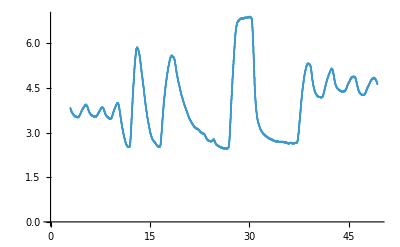

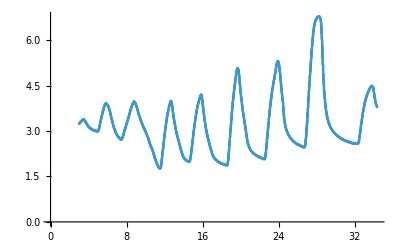

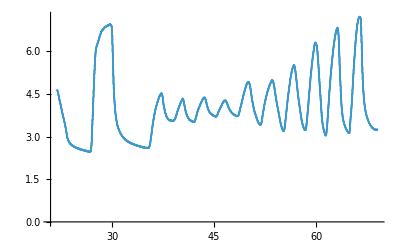

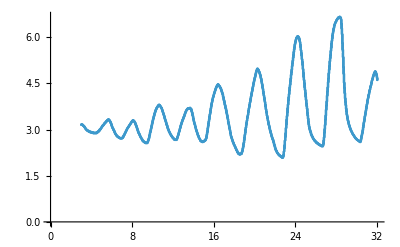

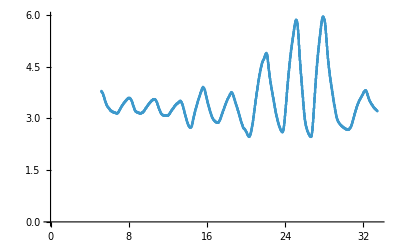

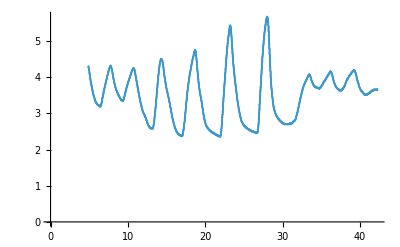

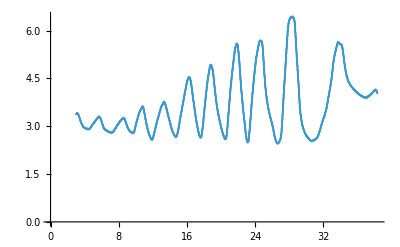

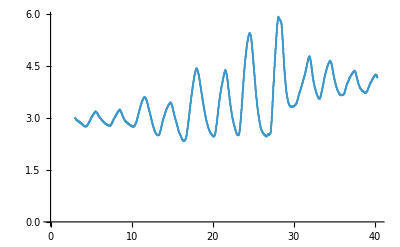

```mathematica
preparePNGData=.
preparePNGData[pngPath_String]:=Module[{points,pxPosition0And1Y,pxPosition0And2X,pxDistanceFor1Liter,pxDistanceFor1S}
,points=PixelValuePositions[Import[pngPath],Blue,.25]; (*get blue pixle points*)

pxPosition0And1Y={{85,203},{84,144}}; (*manually detected 0 and 1 y-values*)
pxPosition0And2X={{859,145},{799,145}}; (*manually detected 0 and 2 x-values*)
pxDistanceFor1Liter=Subtract@@(pxPosition0And1Yᵀ[[2]]); (*factor for volume scaling insted of pixles*)
pxDistanceFor1S=Subtract@@(pxPosition0And2Xᵀ[[1]])/2; (*factor for volume scaling insted of pixles*)

points=Select[points,#[[2]]<550& ] ;(*cut top right curve description*)
points[[All,2]]=points[[All,2]]/pxDistanceFor1Liter 1.; (*replace y pixles values by volumes values*)
points[[All,1]]=points[[All,1]]/pxDistanceFor1S 1.; (*replace x pixles values by second values*)

Print[ListPlot[points]];
SortBy[points,First]]

parts=2;;9
points=preparePNGData[#]&/@(spiroDataPNG[[parts]])
```

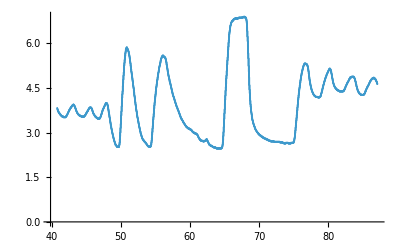
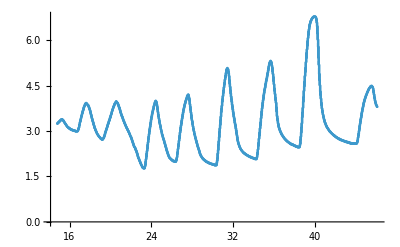
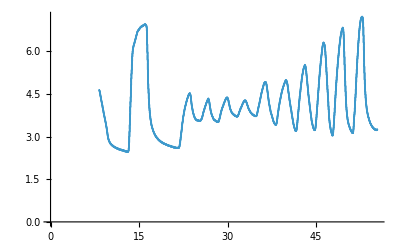
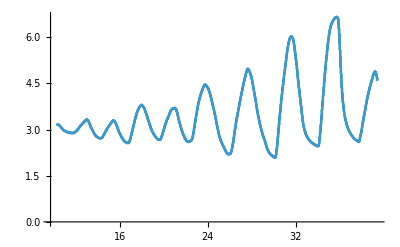
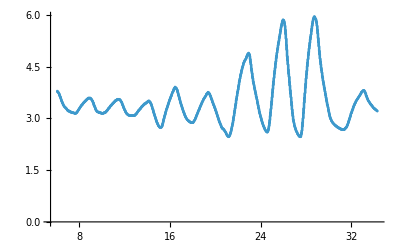
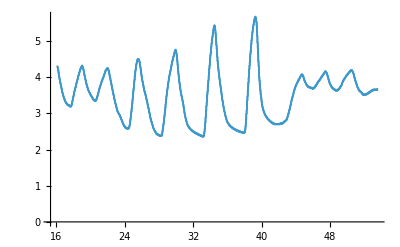
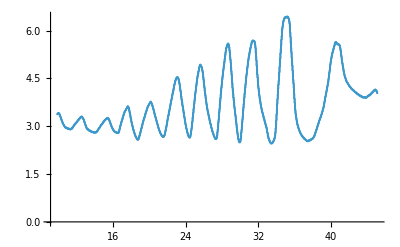
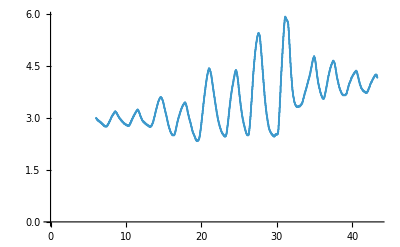

```mathematica
spiroTimeDeltaCorrection=.
spiroTimeDeltaCorrection[list_List]:=Module[{diff,lasttime,temp,tempAll},
Map[(lasttime=#[[2,-1,1]];
diff=#[[1]]-lasttime;
temp=#[[2,All,1]]+diff;
tempAll=#;
tempAll[[2,All,1]]=temp;
#[[-1]]->tempAll[[2]]
)&
,list
]
]

spiroDataTimeCalibrated=spiroTimeDeltaCorrection[Transpose[{times[[parts]][[All,-2]],points,filenames[[parts]]}]];
ListPlot[#[[2]]]&/@spiroDataTimeCalibrated
```

```mathematica
Abs[Subtract@@MinMax@#[[2,All,2]]] &/@spiroDataTimeCalibrated
```

{4.44068,5.01695,4.76271,4.59322,3.49153,3.32203,3.98305,3.59322}

```mathematica
spiroDataTimeCalibrated
```

```mathematica
smoothSpiroData=.
smoothSpiroData[l_]:=l[[1]]->((Normal[Mean[#[[All,2]]]&/@GroupBy[l[[2]],First]]) /. (Rule->List))

spiroDataTimeCalibratedSmoothed=smoothSpiroData[#]&/@spiroDataTimeCalibrated
```

### RIP data

```mathematica
allRIPData=(path=impPath~~#~~".csv";If[FileExistsQ[path],#->Import[path],Nothing])&/@filenames;
```

```mathematica
TableForm[allRIPData[[-1,2,1;;5]]] (*die Datensätze wurden beim Export vom Vernier Programm zusammengehängt. Der letzte Datensatz enthält alle Messreihen!*)
```

Datensatz 1:Zeit(s) | Datensatz 1:Force 1(N) | Datensatz 1:Respiration Rate 1(bpm) | Datensatz 1:Force 2(N) | Datensatz 1:Respiration Rate 2(bpm) | Datensatz 2:Zeit(s) | Datensatz 2:Force 1(N) | Datensatz 2:Respiration Rate 1(bpm) | Datensatz 2:Force 2(N) | Datensatz 2:Respiration Rate 2(bpm) | Datensatz 3:Zeit(s) | Datensatz 3:Force 1(N) | Datensatz 3:Respiration Rate 1(bpm) | Datensatz 3:Force 2(N) | Datensatz 3:Respiration Rate 2(bpm) | Datensatz 4:Zeit(s) | Datensatz 4:Force 1(N) | Datensatz 4:Respiration Rate 1(bpm) | Datensatz 4:Force 2(N) | Datensatz 4:Respiration Rate 2(bpm) | Datensatz 5:Zeit(s) | Datensatz 5:Force 1(N) | Datensatz 5:Respiration Rate 1(bpm) | Datensatz 5:Force 2(N) | Datensatz 5:Respiration Rate 2(bpm) | Datensatz 6:Zeit(s) | Datensatz 6:Force 1(N) | Datensatz 6:Respiration Rate 1(bpm) | Datensatz 6:Force 2(N) | Datensatz 6:Respiration Rate 2(bpm) | Datensatz 7:Zeit(s) | Datensatz 7:Force 1(N) | Datensatz 7:Respiration Rate 1(bpm) | Datensatz 7:Force 2(N) | Datensatz 7:Respiration Rate 2(bpm) | Datensatz 8:Zeit(s) | Datensatz 8:Force 1(N) | Datensatz 8:Respiration Rate 1(bpm) | Datensatz 8:Force 2(N) | Datensatz 8:Respiration Rate 2(bpm) | Datensatz 9:Zeit(s) | Datensatz 9:Force 1(N) | Datensatz 9:Respiration Rate 1(bpm) | Datensatz 9:Force 2(N) | Datensatz 9:Respiration Rate 2(bpm) | Datensatz 10:Zeit(s) | Datensatz 10:Force 1(N) | Datensatz 10:Respiration Rate 1(bpm) | Datensatz 10:Force 2(N) | Datensatz 10:Respiration Rate 2(bpm) | Datensatz 11:Zeit(s) | Datensatz 11:Force 1(N) | Datensatz 11:Respiration Rate 1(bpm) | Datensatz 11:Force 2(N) | Datensatz 11:Respiration Rate 2(bpm) | Datensatz 12:Zeit(s) | Datensatz 12:Force 1(N) | Datensatz 12:Respiration Rate 1(bpm) | Datensatz 12:Force 2(N) | Datensatz 12:Respiration Rate 2(bpm) | Datensatz 13:Zeit(s) | Datensatz 13:Force 1(N) | Datensatz 13:Respiration Rate 1(bpm) | Datensatz 13:Force 2(N) | Datensatz 13:Respiration Rate 2(bpm) | Datensatz 14:Zeit(s) | Datensatz 14:Force 1(N) | Datensatz 14:Respiration Rate 1(bpm) | Datensatz 14:Force 2(N) | Datensatz 14:Respiration Rate 2(bpm) | Datensatz 15:Zeit(s) | Datensatz 15:Force 1(N) | Datensatz 15:Respiration Rate 1(bpm) | Datensatz 15:Force 2(N) | Datensatz 15:Respiration Rate 2(bpm) | Datensatz 16:Zeit(s) | Datensatz 16:Force 1(N) | Datensatz 16:Respiration Rate 1(bpm) | Datensatz 16:Force 2(N) | Datensatz 16:Respiration Rate 2(bpm) | Datensatz 17:Zeit(s) | Datensatz 17:Force 1(N) | Datensatz 17:Respiration Rate 1(bpm) | Datensatz 17:Force 2(N) | Datensatz 17:Respiration Rate 2(bpm) | Datensatz 18:Zeit(s) | Datensatz 18:Force 1(N) | Datensatz 18:Respiration Rate 1(bpm) | Datensatz 18:Force 2(N) | Datensatz 18:Respiration Rate 2(bpm) | Datensatz 19:Zeit(s) | Datensatz 19:Force 1(N) | Datensatz 19:Respiration Rate 1(bpm) | Datensatz 19:Force 2(N) | Datensatz 19:Respiration Rate 2(bpm)
0. | 14.8856 | 22.3729 | 12.2965 | 22.3577 | 0. | 10.5293 | 21.398 | 8.47167 | 21.4133 | 0. | 12.8084 | 20.7612 | 10.1018 | 20.7756 | 0. | 14.3618 | 0. | 10.9091 | 14.4578 | 0. | 16.2346 | 22.0147 | 11.2106 | 18.012 | 0. | 12.5554 | 21.9619 | 8.96478 | 21.9619 | 0. | 10.3147 | 9.91736 | 8.25705 | 9.90099 | 0. | 10.7439 | 16.632 | 9.34293 | 14.5935 | 0. | 10.0387 | 20.3313 | 7.38835 | 20.4255 | 0. | 11.2626 | 21.2598 | 7.75627 | 20.2551 | 0. | 12.6704 | 12.5174 | 8.97756 | 12.4138 | 0. | 10.5651 | 0. | 7.99644 | 0. | 0. | 12.3331 | 0 | 9.44768 | 19.4384 | 0. | 8.64626 | 0. | 7.12774 | 19.4085 | 0. | 9.85989 | 6.23701 | 7.5672 | 0 | 0. | 7.91808 | 6.85453 | 6.67551 | 14.7472 | 0. | 12.2999 | 8.79765 | 8.49467 | 17.2579 | 0. | 10.7541 | 21.7077 | 7.83037 | 20.0267 | 0. | 7.17203 | 0. | 6.34846 | 8.44278
0.1 | 13.9734 | Missing[NotAvailable] | 11.7421 | Missing[NotAvailable] | 0.1 | 11.5896 | Missing[NotAvailable] | 9.11553 | Missing[NotAvailable] | 0.1 | 11.4798 | Missing[NotAvailable] | 9.38636 | Missing[NotAvailable] | 0.1 | 12.6985 | Missing[NotAvailable] | 9.93568 | Missing[NotAvailable] | 0.1 | 16.7405 | Missing[NotAvailable] | 11.4252 | Missing[NotAvailable] | 0.1 | 14.1318 | Missing[NotAvailable] | 9.93313 | Missing[NotAvailable] | 0.1 | 9.73213 | Missing[NotAvailable] | 8.06032 | Missing[NotAvailable] | 0.1 | 9.45109 | Missing[NotAvailable] | 8.49722 | Missing[NotAvailable] | 0.1 | 11.679 | Missing[NotAvailable] | 8.25705 | Missing[NotAvailable] | 0.1 | 10.7107 | Missing[NotAvailable] | 7.79971 | Missing[NotAvailable] | 0.1 | 11.237 | Missing[NotAvailable] | 8.55598 | Missing[NotAvailable] | 0.1 | 11.0837 | Missing[NotAvailable] | 8.11141 | Missing[NotAvailable] | 0.1 | 11.5462 | Missing[NotAvailable] | 8.95712 | Missing[NotAvailable] | 0.1 | 8.19658 | Missing[NotAvailable] | 6.81603 | Missing[NotAvailable] | 0.1 | 9.47408 | Missing[NotAvailable] | 7.2376 | Missing[NotAvailable] | 0.1 | 7.59104 | Missing[NotAvailable] | 6.69083 | Missing[NotAvailable] | 0.1 | 13.0639 | Missing[NotAvailable] | 8.88814 | Missing[NotAvailable] | 0.1 | 9.90332 | Missing[NotAvailable] | 7.37813 | Missing[NotAvailable] | 0.1 | 7.20013 | Missing[NotAvailable] | 6.43533 | Missing[NotAvailable]
0.2 | 12.7036 | Missing[NotAvailable] | 10.9117 | Missing[NotAvailable] | 0.2 | 13.0996 | Missing[NotAvailable] | 9.97146 | Missing[NotAvailable] | 0.2 | 10.1052 | Missing[NotAvailable] | 8.67352 | Missing[NotAvailable] | 0.2 | 10.772 | Missing[NotAvailable] | 8.70928 | Missing[NotAvailable] | 0.2 | 16.7865 | Missing[NotAvailable] | 11.415 | Missing[NotAvailable] | 0.2 | 16.135 | Missing[NotAvailable] | 11.0011 | Missing[NotAvailable] | 0.2 | 9.13426 | Missing[NotAvailable] | 7.81248 | Missing[NotAvailable] | 0.2 | 8.06883 | Missing[NotAvailable] | 7.50077 | Missing[NotAvailable] | 0.2 | 13.7614 | Missing[NotAvailable] | 9.34037 | Missing[NotAvailable] | 0.2 | 10.0106 | Missing[NotAvailable] | 7.70773 | Missing[NotAvailable] | 0.2 | 9.54307 | Missing[NotAvailable] | 7.96067 | Missing[NotAvailable] | 0.2 | 11.0658 | Missing[NotAvailable] | 8.12164 | Missing[NotAvailable] | 0.2 | 10.4859 | Missing[NotAvailable] | 8.2826 | Missing[NotAvailable] | 0.2 | 7.71624 | Missing[NotAvailable] | 6.45833 | Missing[NotAvailable] | 0.2 | 9.36421 | Missing[NotAvailable] | 6.87735 | Missing[NotAvailable] | 0.2 | 7.58849 | Missing[NotAvailable] | 6.76237 | Missing[NotAvailable] | 0.2 | 13.5519 | Missing[NotAvailable] | 9.13086 | Missing[NotAvailable] | 0.2 | 8.79189 | Missing[NotAvailable] | 6.8518 | Missing[NotAvailable] | 0.2 | 7.43008 | Missing[NotAvailable] | 6.78537 | Missing[NotAvailable]
0.3 | 12.0623 | Missing[NotAvailable] | 10.4084 | Missing[NotAvailable] | 0.3 | 14.0271 | Missing[NotAvailable] | 10.393 | Missing[NotAvailable] | 0.3 | 9.91354 | Missing[NotAvailable] | 8.57642 | Missing[NotAvailable] | 0.3 | 10.4015 | Missing[NotAvailable] | 8.35414 | Missing[NotAvailable] | 0.3 | 16.02 | Missing[NotAvailable] | 11.0292 | Missing[NotAvailable] | 0.3 | 17.0292 | Missing[NotAvailable] | 11.2566 | Missing[NotAvailable] | 0.3 | 9.07294 | Missing[NotAvailable] | 7.70006 | Missing[NotAvailable] | 0.3 | 7.9513 | Missing[NotAvailable] | 7.26315 | Missing[NotAvailable] | 0.3 | 14.7604 | Missing[NotAvailable] | 9.64442 | Missing[NotAvailable] | 0.3 | 9.96208 | Missing[NotAvailable] | 7.54676 | Missing[NotAvailable] | 0.3 | 9.11893 | Missing[NotAvailable] | 7.53654 | Missing[NotAvailable] | 0.3 | 9.96208 | Missing[NotAvailable] | 7.88402 | Missing[NotAvailable] | 0.3 | 9.93143 | Missing[NotAvailable] | 8.03477 | Missing[NotAvailable] | 0.3 | 7.71368 | Missing[NotAvailable] | 6.48132 | Missing[NotAvailable] | 0.3 | 9.8139 | Missing[NotAvailable] | 6.93101 | Missing[NotAvailable] | 0.3 | 8.49807 | Missing[NotAvailable] | 7.03065 | Missing[NotAvailable] | 0.3 | 12.8876 | Missing[NotAvailable] | 8.87791 | Missing[NotAvailable] | 0.3 | 8.25279 | Missing[NotAvailable] | 6.72916 | Missing[NotAvailable] | 0.3 | 7.95386 | Missing[NotAvailable] | 7.32958 | Missing[NotAvailable]

```mathematica
ripData=Transpose[{allRIPData[[All,1]],allRIPData[[All,2,All,-5;;-1]][[All,All,{1,2,4}]]}]
```

```mathematica
ripData=#[[1]]->#[[2]]&/@(Transpose[{allRIPData[[All,1]],allRIPData[[All,2,All,-5;;-1]][[All,2;;-1,{1,2,4}]]}]/.({Missing["NotAvailable"],Missing["NotAvailable"],Missing["NotAvailable"]}->Nothing))
```

```mathematica
Transpose[{ filenames,times}]
```

{{13-52,{0.,11.587,86.626,163.838}},{13-58,{0.,10.215,87.148,96.617}},{14-07,{0.,7.21,46.161,95.607}},{14-09,{0.,6.607,55.385,76.168}},{14-12,{0.,6.155,39.394,51.1}},{14-16,{0.,4.767,34.314,45.389}},{14-18,{0.,16.13,53.533,60.223}},{14-21,{0.,5.265,45.151,69.111}},{14-25,{0.,4.027,43.35,48.236}},{14-28,{0.,4.538,32.585,48.87}},{14-30,{0.,4.698,34.442,48.932}},{14-34,{0.,18.158,64.024,77.825}}}

```mathematica
{#[[1]],#[[2,-1,1]]}&/@(ripData/.({Missing["NotAvailable"],Missing["NotAvailable"],Missing["NotAvailable"]}->Nothing))
(*die Zeiten der RIP Messungen sind "Taktgeber" und synchron*)
```

{{13-52,163.2},{13-58,95.9},{14-07,94.8},{14-09,75.5},{14-18,59.4},{14-21,68.5},{14-28,48.2},{14-30,48.1},{14-34,77.1}}

### Evaluation

```mathematica
Length@spiroDataTimeCalibratedSmoothed
Length@ripData
spiroDataTimeCalibratedSmoothed[[All,1]]
ripData[[All,1]]
evaluableData=Intersection[spiroDataTimeCalibrated[[All,1]],ripData[[All,1]]]
```

8

9

{13-58,14-07,14-09,14-12,14-16,14-18,14-21,14-25}

{13-52,13-58,14-07,14-09,14-18,14-21,14-28,14-30,14-34}

{13-58,14-07,14-09,14-18,14-21}

```mathematica
calibrateXMin=.
calibrateXMin[spiro_List]:=Module[{lowestVolumes,lowestForce}
,lowestVolumes=Min[spiro[[All,2]]]
]
calibrateXMin[spiroDataTimeCalibratedSmoothed[[-1,2]]]
```

2.33051

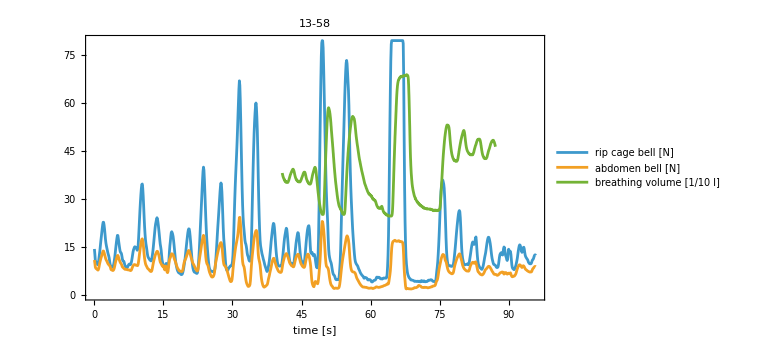
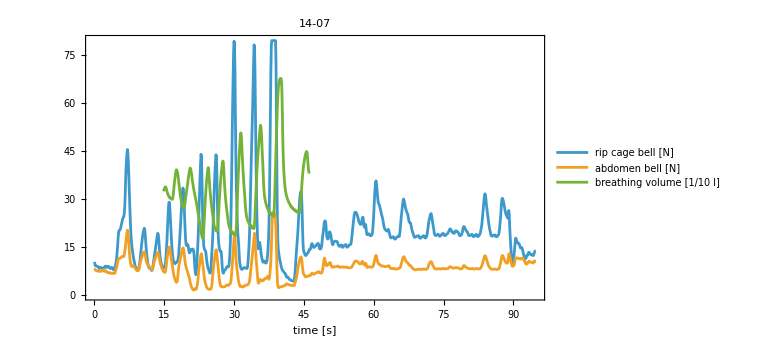
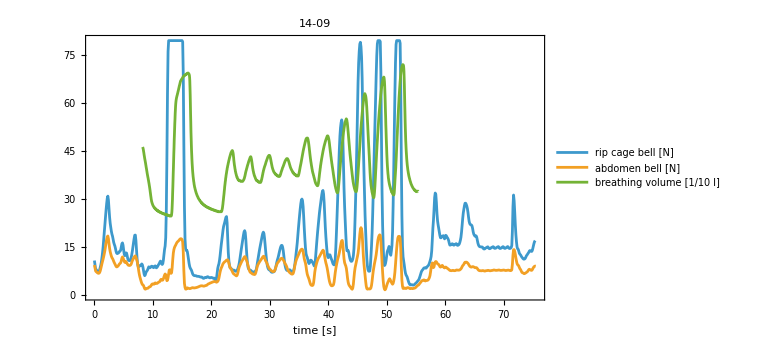
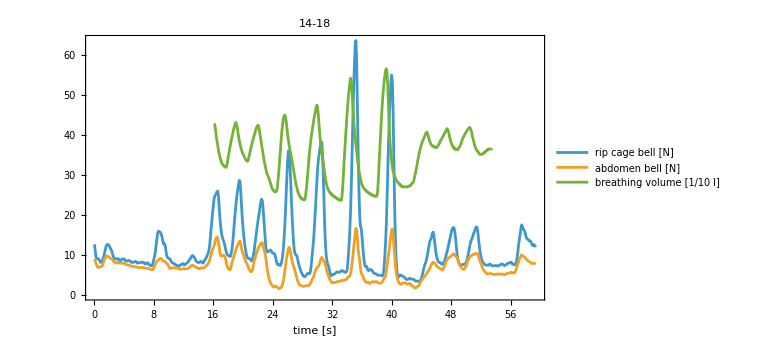
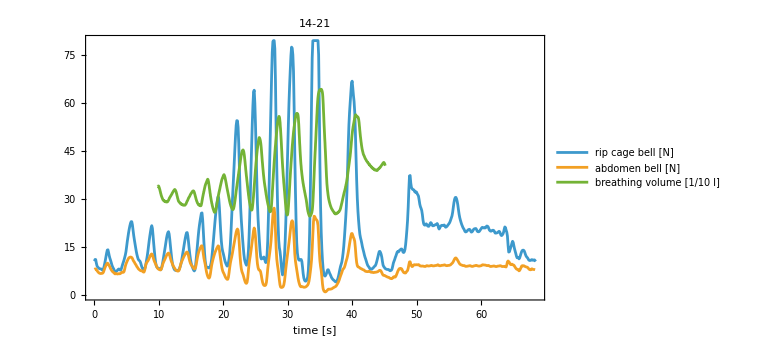

```mathematica
dataForAnalysis=Transpose[{evaluableData,evaluableData/.ripData,evaluableData /. spiroDataTimeCalibratedSmoothed}];
dataForAnalysis[[All,2]]=Map[Transpose[{{#[[1]],#[[2]]},{#[[1]],#[[3]]}}&/@(Flatten[#,1])] /. Missing["NotAvailable"]->Null&,dataForAnalysis[[All,{2}]]];

ListPlot[Append[#[[2]],{#[[1]],#[[2]]*10}&/@#[[3]]],PlotLabel->myStyle@#[[1]],PlotRange->All,PlotLegends->{"rip cage bell [N]","abdomen bell [N]","breathing volume [1/10 l]"},FrameLabel->{"time [s]",None},ImageSize->Large,Frame->True,Joined->True,myFrameStyle[],myFrameTickStyle[], myPlotStyle[]]&/@dataForAnalysis
```

```mathematica
dataForAnalysis={#[[1]],Append[#[[2]],#[[3]]]}&/@dataForAnalysis (*time stamp, {rip, abdomen, spiro}*)
```

{{{41.8813,3.51695},{43.1813,3.9322}},{{44.5147,3.5339},{45.648,3.83898}},{{46.8147,3.4661},{47.9147,3.99153}},{{49.6147,2.51695},{50.8813,5.85593}},{{54.2147,2.51695},{56.1147,5.58475}},{{64.2147,2.4661},{67.8147,6.88136}},{{74.4147,2.63559},{76.6813,5.31356}},{{78.648,4.17797},{80.248,5.14407}},{{81.9147,4.38136},{83.5813,4.87288}},{{84.9813,4.26271},{86.648,4.83898}}}

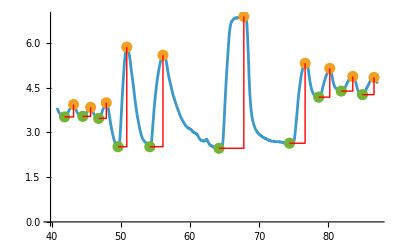

```mathematica
values=dataForAnalysis[[1,2,3]];
peaks=FindPeaks[dataForAnalysis[[1,2,3]][[All,2]],10];
peaksLow=FindPeaks[-dataForAnalysis[[1,2,3]][[All,2]],10];

If[peaks[[1,1]]<peaksLow[[1,1]],peaks=Delete[peaks,1],Nothing] ;(*start with first inspiration volume*)

peaksLow=peaksLow[[1;;Length[peaks]]];


peaksLow=peaksLow[[1;;Length[peaks]]];

xdiffs=Transpose[{values[[Round[#[[1]]]]]&/@peaksLow,values[[Round[#[[1]]]]]&/@peaks}]
xdiffsLine={#[[1]],{#[[2,1]],
#[[1,2]]},#[[2]]}&/@xdiffs;
linesDiff=Line/@xdiffsLine;
xDiffSeconds=-Subtract@@@xdiffs[[All,All,1]]; (*inspiratory breathing duration*)
yDiffVolume=-Subtract@@@xdiffs[[All,All,2]] ;(*inspiratory breathing volume*)

Tabular[Transpose[{xDiffSeconds,yDiffVolume}],{"Δ insp. time [s]","Δ insp. volume [l]"}]

Show[
ListLinePlot[
{values,values[[Round@#]]&/@ peaks[[All,1]],values[[Round@#]]&/@ peaksLow[[All,1]]},
Joined->{True,False,False},
PlotStyle->{Automatic,PointSize[.02],PointSize[.02],PlotRange->All}
]
,Graphics[{Thick,Red,#}]&/@linesDiff
]
```

breaths from spirometry

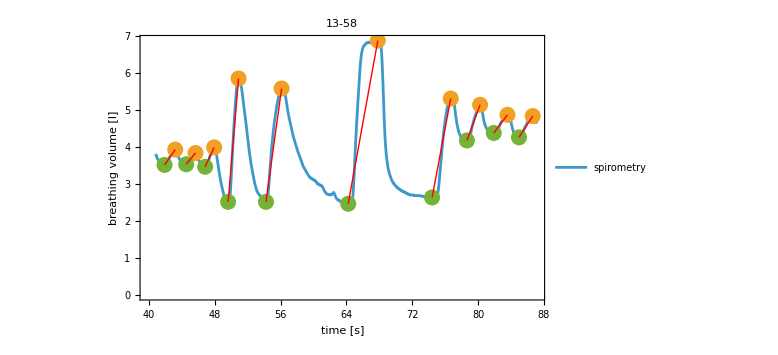
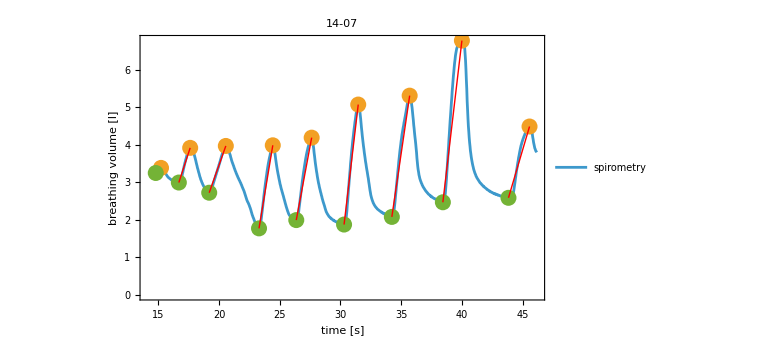
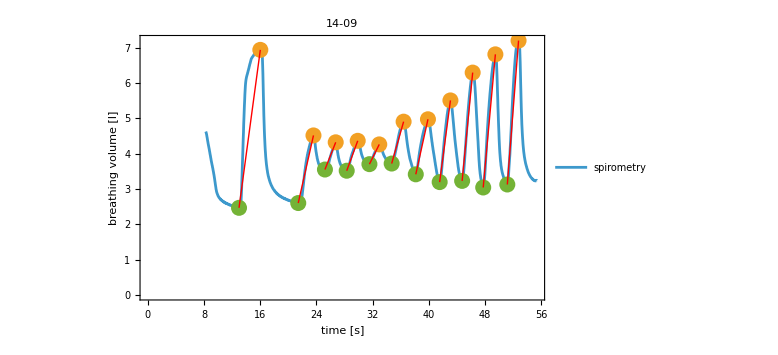
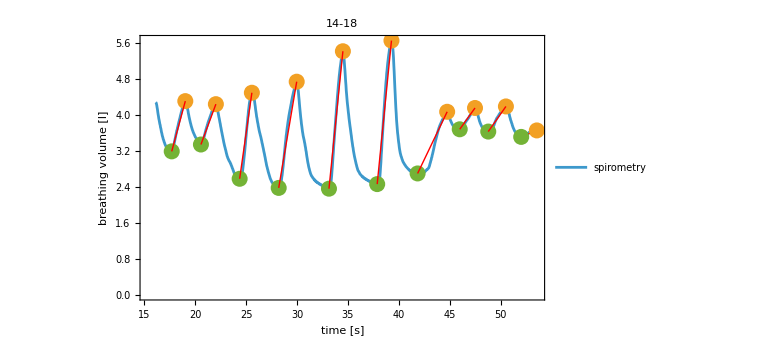
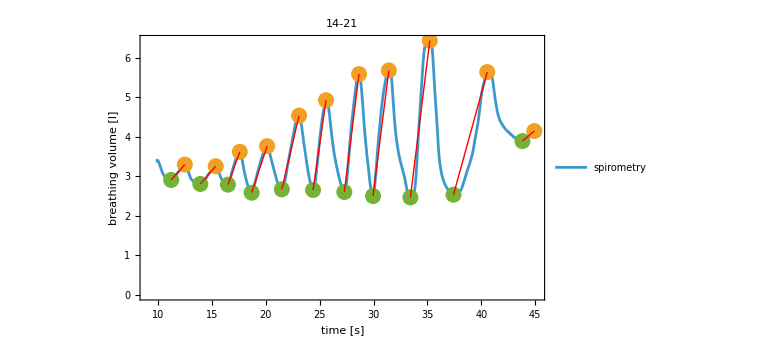

```mathematica
breathDetect=.
breathDetect[l_]:=Module[{peaks,peaksLow,xdiffs,linesDiff,xDiffSeconds,yDiffVolume}
,values=l[[2,3]];
peaks=FindPeaks[l[[2,3]][[All,2]],10];
peaksLow=FindPeaks[-l[[2,3]][[All,2]],10];

If[peaks[[1,1]]<peaksLow[[1,1]],peaks=Delete[peaks,1],Nothing] ;(*start with first inspiration volume*)

peaksLow=peaksLow[[1;;Length[peaks]]];


peaksLow=peaksLow[[1;;Length[peaks]]];

xdiffs=Transpose[{values[[Round[#[[1]]]]]&/@peaksLow,values[[Round[#[[1]]]]]&/@peaks}];
linesDiff=Line/@xdiffs;
xDiffSeconds=-Subtract@@@xdiffs[[All,All,1]]; (*inspiratory breathing duration*)
yDiffVolume=-Subtract@@@xdiffs[[All,All,2]] ;(*inspiratory breathing volume*)

{Tabular[Transpose[{xDiffSeconds,yDiffVolume}],{"Δ insp. time [s]","Δ insp. volume [l]"}],

Show[
ListLinePlot[
{values,values[[Round@#]]&/@ peaks[[All,1]],values[[Round@#]]&/@ peaksLow[[All,1]]},PlotLabel->myStyle@l[[1]],PlotLegends->{"spirometry"},FrameLabel->{"time [s]","breathing volume [l]"},
Joined->{True,False,False},
PlotStyle->{Automatic,PointSize[.02],PointSize[.02],PlotRange->All},ImageSize->Large,Frame->True,myFrameStyle[],myFrameTickStyle[]
]
,Graphics[{Thick,Red,#}]&/@linesDiff
]}
]

spiroBreaths=breathDetect/@ dataForAnalysis
```

breaths from RIP

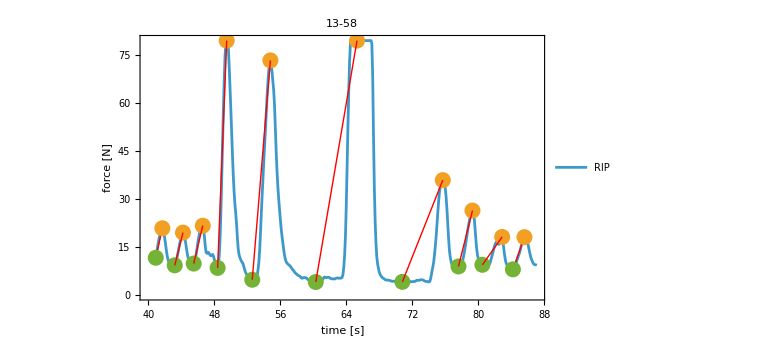
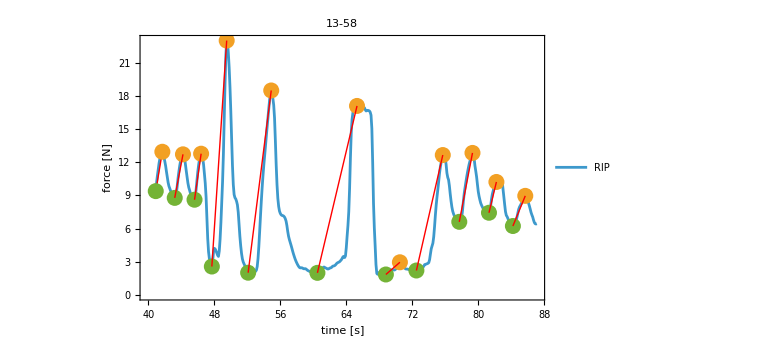
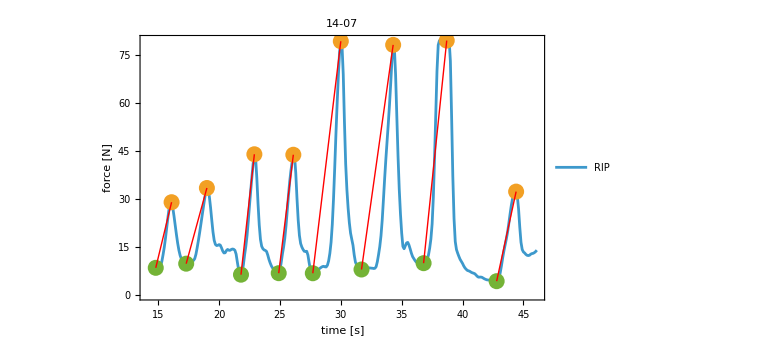
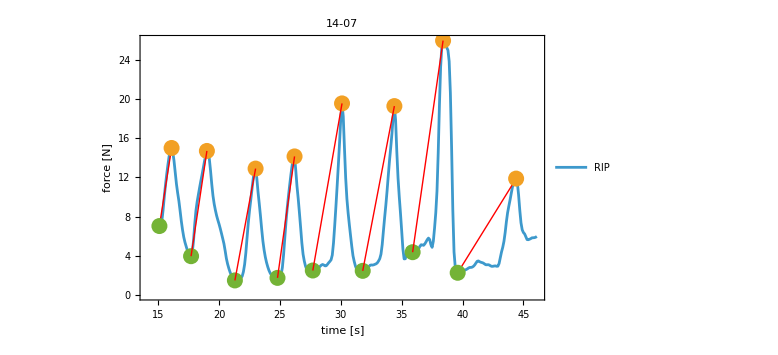
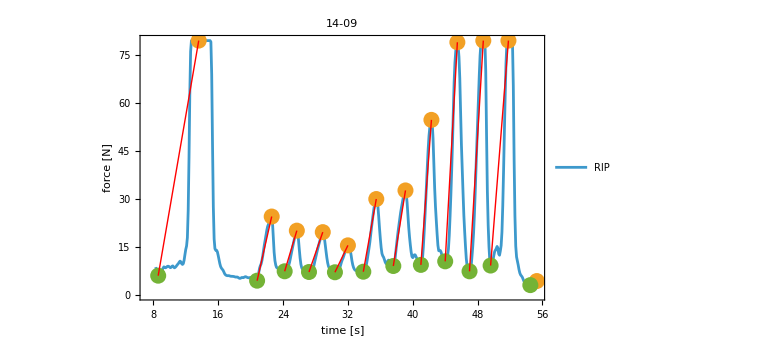
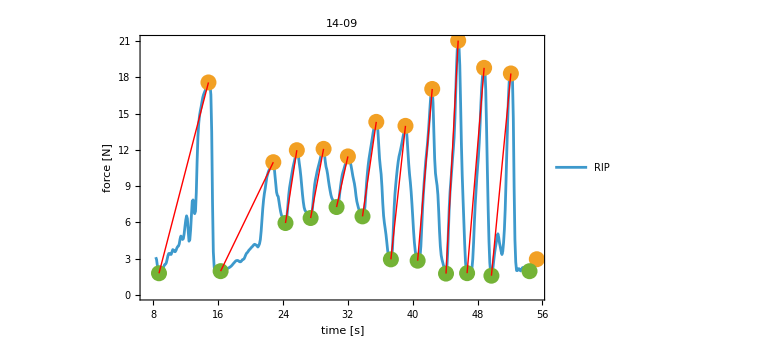
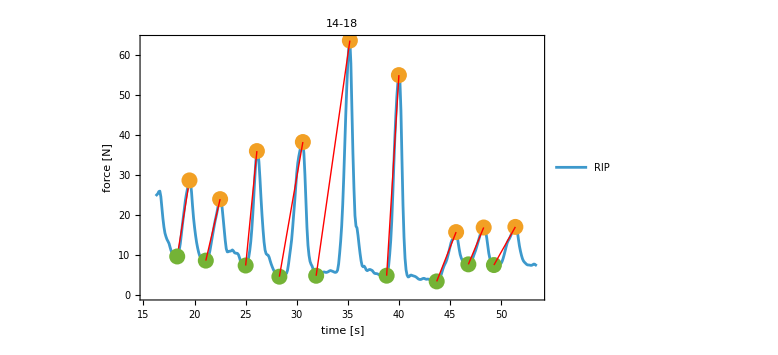
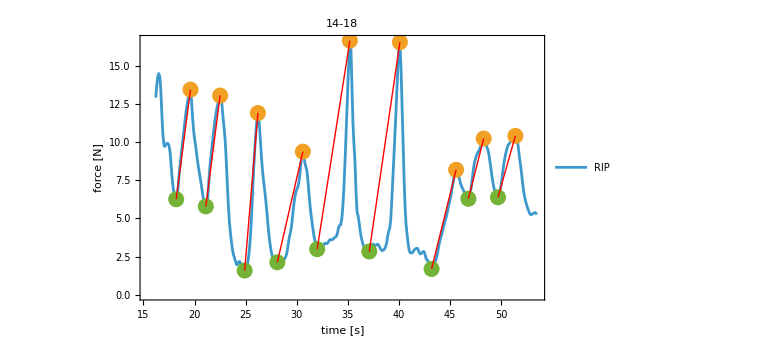

```mathematica
dataForAnalysisCropped=dataForAnalysis;
Table[
{lbound,ubound}=dataForAnalysisCropped[[i,2,3]][[{1,-1}]][[All,1]];
dataForAnalysisCropped[[i,2,1]]=Select[dataForAnalysisCropped[[i,2,1]],lbound<#[[1]]<ubound&];
dataForAnalysisCropped[[i,2,2]]=Select[dataForAnalysisCropped[[i,2,2]],lbound<#[[1]]<ubound&];
,{i,Length@dataForAnalysisCropped}];

breathDetect=.
breathDetect[l_]:=Module[{peaks,peaksLow,xdiffs,linesDiff,xDiffSeconds,yDiffVolume}
,
Table[values=l[[2,i]];
peaks=FindPeaks[l[[2,i]][[All,2]],6];
peaksLow=FindPeaks[-l[[2,i]][[All,2]],6];

If[peaks[[1,1]]<peaksLow[[1,1]],peaks=Delete[peaks,1],Nothing] ;(*start with first inspiration volume*)
(*hier noch prüfen, ob der Peak im Zeitverlauf auch nahe am Peak der Spirometrie liegt!!! 10%?*)
peaksLow=peaksLow[[1;;Length[peaks]]];


peaksLow=peaksLow[[1;;Length[peaks]]];

xdiffs=Transpose[{values[[Round[#[[1]]]]]&/@peaksLow,values[[Round[#[[1]]]]]&/@peaks}];
linesDiff=Line/@xdiffs;
xDiffSeconds=-Subtract@@@xdiffs[[All,All,1]]; (*inspiratory breathing duration*)
yDiffVolume=-Subtract@@@xdiffs[[All,All,2]] ;(*inspiratory breathing volume*)

{Tabular[Transpose[{xDiffSeconds,yDiffVolume}],{"Δ insp. time [s]","Δ force [N]"}]
,Show[
ListLinePlot[
{values,values[[Round@#]]&/@ peaks[[All,1]],values[[Round@#]]&/@ peaksLow[[All,1]]},PlotLabel->myStyle@l[[1]],
PlotLegends->{"RIP"},FrameLabel->{"time [s]","force [N]"},
Joined->{True,False,False},
PlotStyle->{Automatic,PointSize[.02],PointSize[.02],PlotRange->All},ImageSize->Large,Frame->True,PlotRange->All,myFrameStyle[],myFrameTickStyle[]
]
,Graphics[{Thick,Red,#}]&/@linesDiff
]
}
,{i,{1,2}}]

]

ripBreaths=breathDetect/@dataForAnalysisCropped
```

```mathematica
Transpose[{spiroBreaths[[All,2]],ripBreaths[[All,All,2]]}]
```

{{-Graphics-,{-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-}}}

```mathematica
dCorrelation=Flatten/@Transpose[{spiroBreaths[[All,1]],ripBreaths[[All,All,1]]}]
```

{{,,},{,,},{,,},{,,},{,,}}

```mathematica
myTabularNormal=.
myTabularNormal[t_]:=Module[{},If[TabularQ[t],Values/@(Normal@t),Values/@(Normal/@t)]]
```

```mathematica
spiroBreaths[[1,2]]
```

-Graphics-

```mathematica
myPlotLabelAndLegend[plotLabel_,plotLegend_List,frameLabel_List]:=Sequence[PlotLabel->myStyle@plotLabel,
PlotLegends->myStyle/@plotLegend,FrameLabel->frameLabel]
```

```mathematica
myPlotConfig=.
myPlotConfig=Sequence[PlotRange->All,Frame->True,ImageSize->Large,myFrameStyle[],myFrameTickStyle[]]
```

Sequence[PlotRange→All,Frame→True,ImageSize→Large,FrameStyle→Directive[FontSize→13,FontFamily→Lucida Sans Unicode,GrayLevel[0]],FrameTicksStyle→Directive[FontSize→13,FontFamily→Lucida Sans Unicode,GrayLevel[0]]]

```mathematica
myPlotLabelAndLegend["13-58",{"correlation spirometry and RIP"},{"force [N]","breathing volume [l]"}]
```

Sequence[PlotLabel→13-58,PlotLegends→{correlation spirometry and RIP},FrameLabel→{force [N],breathing volume [l]}]

{10,10,10}

{{{1.3,0.8,0.8},{0.415254,9.22866,3.55912}},{{1.13333,1.,1.},{0.305085,10.2353,3.93726}},{{1.1,1.1,0.8},{0.525424,11.845,4.15954}},{{1.26667,1.1,1.8},{3.33898,71.1057,20.4221}},{{1.9,2.2,2.8},{3.0678,68.6171,16.4721}},{{3.6,5.,4.8},{4.41525,75.5309,15.0873}},{{2.26667,4.9,3.2},{2.67797,31.8302,10.4372}},{{1.6,1.7,1.6},{0.966102,17.4915,6.22909}},{{1.66667,2.4,0.9},{0.491525,8.71255,2.78239}},{{1.66667,1.4,1.5},{0.576271,10.0641,2.72619}}}

FittedModel[…]

{0.0659819+0.0512292 x-2.306 √(0.0500649-0.00182165 x+0.0000289463 x^2),0.0659819+0.0512292 x+2.306 √(0.0500649-0.00182165 x+0.0000289463 x^2)}

{,}

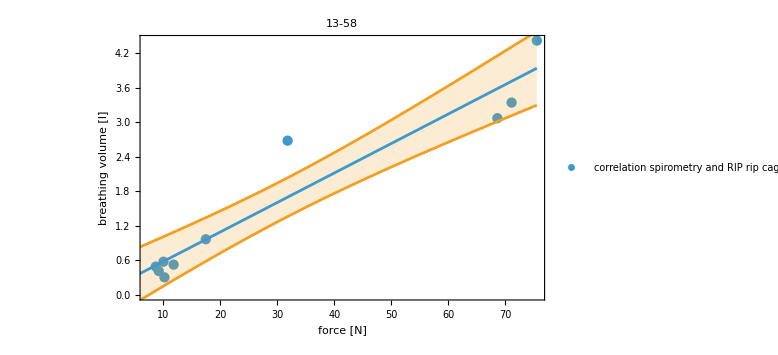

```mathematica
temp=myTabularNormal[dCorrelation[[1]]];
temp[[3]] = Select[temp[[3]],#[[2]]>1.5&];
Length/@temp
temp=Transpose/@Transpose[temp]
lnm=LinearModelFit[temp[[All,2]][[All,{2,1}]],x,x]
lnm["MeanPredictionBands",ConfidenceLevel->.95]
lnm[{"ParameterEstimates","MeanPredictions"}]
bands95[x_]=lnm["MeanPredictionBands",ConfidenceLevel->.95];

Show[ListPlot[temp[[All,2]][[All,{2,1}]],myPlotLabelAndLegend["13-58",{"correlation spirometry and RIP rip cage"},{"force [N]","breathing volume [l]"}],myPlotConfig],Plot[{lnm[x],bands95[x]},{x,Min@temp[[All,2]][[All,{2,1}]],Max@temp[[All,2]][[All,{2,1}]]},Filling->{2->{1}}]]
```

manuelle Anpassung, siehe auch Transpose[{spiroBreaths[[All,2]],ripBreaths[[All,All,2]]}]

13 - 58 delete 7 bei abdomen
14-07 delete 1 bei spiro
14 - 09 delete - 1 bei cage und abdomen
14 - 18 delete - 1 bei spirometry
14-21 delete -1 bei spirometry und cage

```mathematica
evaluableData
```

{13-58,14-07,14-09,14-18,14-21}

```mathematica
dCorrelationElected=myTabularNormal/@dCorrelation;
dCorrelationElected=Delete[dCorrelationElected,{{1,3,7},{2,1,1},{3,2,-1},{3,3,-1},{4,1,-1},{5,1,-1},{5,2,-1}}];
Map[Length,dCorrelationElected,{2}]
dCorrelationElected=myFlatten[Transpose[dCorrelationElected][[All,All,All,2]],1];
```

{{10,10,10},{8,8,8},{11,11,11},{9,9,9},{10,10,10}}

```mathematica
Min@fitData[[All,1]]
```

8.41872

FittedModel[…]

FittedModel[…]

{0.90628,0.904242}

0.156586

{{0.181881+0.0487349 x-2.0129 √(0.0106415-0.000396996 x+5.33942×10^-6 x^2),0.181881+0.0487349 x+2.0129 √(0.0106415-0.000396996 x+5.33942×10^-6 x^2)},}

{,}

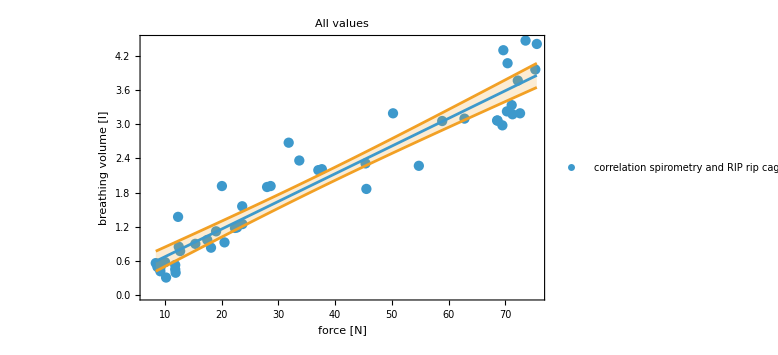

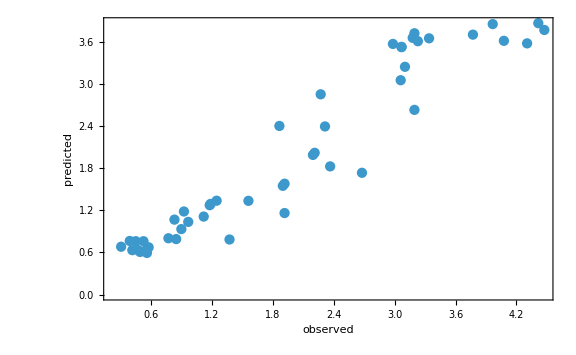

```mathematica
lnmRipCageGetForce=LinearModelFit[Transpose[dCorrelationElected[[{1,2}]]],x,x] (*volume in Newton out*)
fitData=Transpose[dCorrelationElected[[{2,1}]]];
lnmRipCageGetVolume=lnm=LinearModelFit[fitData,x,x]
lnm[{"RSquared","AdjustedRSquared"}]
lnm["EstimatedVariance"]
lnm[{"MeanPredictionBands","SinglePredictions"},ConfidenceLevel->.95] (*https://www.graphpad.com/support/faqid/1506/  Prediciton = wo die nächsten Datenpunkte mit 95% Wahrscheinlichkeit liegen werden, Confidence = wo die aktuellen Daten zu 95% liegen and https://en.wikipedia.org/wiki/Confidence_and_prediction_bands#Prediction_bands*)
lnm[{"ParameterEstimates","MeanPredictions"}]
bands95[x_]=lnm["MeanPredictionBands",ConfidenceLevel->.95];

Show[ListPlot[fitData,myPlotLabelAndLegend["All values",{"correlation spirometry and RIP rip cage"},{"force [N]","breathing volume [l]"}],myPlotConfig],Plot[{lnm[x],bands95[x]},{x,Min@fitData[[All,1]],Max@fitData[[All,1]]},Filling->{2->{1}}]]

ListPlot[Transpose[lnm[{"Response","PredictedResponse"}]],FrameLabel->{"observed","predicted"},myPlotConfig]
```

FittedModel[…]

FittedModel[…]

{0.773369,0.768442}

0.37865

{{-0.123767+0.187762 x-2.0129 √(0.0364504-0.00506547 x+0.000224591 x^2),-0.123767+0.187762 x+2.0129 √(0.0364504-0.00506547 x+0.000224591 x^2)},}

{,}

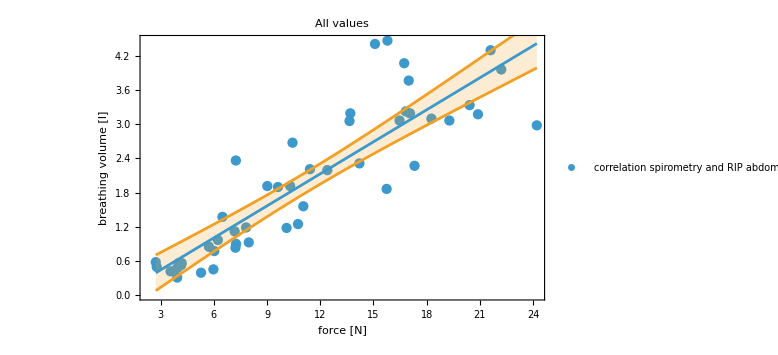

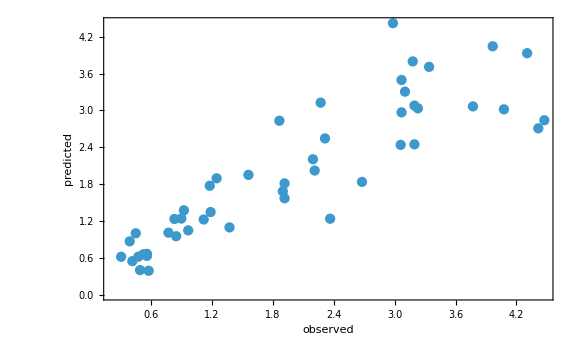

```mathematica
lnmAbdomenGetForce=LinearModelFit[Transpose[dCorrelationElected[[{1,3}]]],x,x]
fitData=Transpose[dCorrelationElected[[{3,1}]]];
lnmAbdomenGetVolume=lnm=LinearModelFit[fitData,x,x]
lnm[{"RSquared","AdjustedRSquared"}]
lnm["EstimatedVariance"]
lnm[{"MeanPredictionBands","SinglePredictions"},ConfidenceLevel->.95]
lnm[{"ParameterEstimates","MeanPredictions"}]
bands95[x_]=lnm["MeanPredictionBands",ConfidenceLevel->.95];

Show[ListPlot[fitData,myPlotLabelAndLegend["All values",{"correlation spirometry and RIP abdomen"},{"force [N]","breathing volume [l]"}],myPlotConfig],Plot[{lnm[x],bands95[x]},{x,Min@fitData[[All,1]],Max@fitData[[All,1]]},Filling->{2->{1}}]]

ListPlot[Transpose[lnm[{"Response","PredictedResponse"}]],FrameLabel->{"observed","predicted"},myPlotConfig]
```

```mathematica
newtonFromRIPripcage=.
newtonFromRIPripcage[v_]:=Module[{},Around[lnmRipCageGetForce[v],(Subtract@@Reverse@(lnmRipCageGetForce["MeanPredictionBands",ConfidenceLevel->.95] /. x->v))/2]]
{#,newtonFromRIPcage[#]}&/@{3,5}
```

{{3,55.92.9},{5,93.6.}}

```mathematica
volumeFromRIPripcage=.
volumeFromRIPripcage[f_]:=Module[{},Around[lnmRipCageGetVolume[f],(Subtract@@Reverse@(lnmRipCageGetVolume["MeanPredictionBands",ConfidenceLevel->.95] /. x->f))/2]]
{#,newtonFromRIPcage[#]}&/@{20,40,60}
```

{{20,372.32.},{40,744.67.},{60,1116.103.}}

-Graphics--Graphics-
aus
 https://publikationen.dguv.de/widgets/pdf/download/article/1011%7CDGUV-Regel112-190_Benutzung-von-Atemschutzgeraeten_Download.pdf

Zielwerte: 30 und 50 l/min  Atemminutenvolumen

```mathematica
af=Range[10,70,5] (*Atemfrequenz*)
```

{10,15,20,25,30,35,40,45,50,55,60,65,70}

```mathematica
Print[myStyle["values for 30 l/min"]]
TableForm[{af,30./af,newtonFromRIPripcage/@(30./af)},TableHeadings->{{"respiratory rate [min^-1 ]","breathing volume [l]","force of RIP of ripcage [N]"},None}]
```

values for 30 l/min

respiratory rate [min^-1 ] | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60
breathing volume [l] | 3. | 2. | 1.5 | 1.2 | 1. | 0.857143 | 0.75 | 0.666667 | 0.6 | 0.545455 | 0.5
force of RIP of ripcage [N] | 55.92.9 | 37.32.2 | 28.02.4 | 22.42.7 | 18.72.9 | 16.03.0 | 14.03.1 | 12.53.3 | 11.33.3 | 10.23.4 | 9.43.5

```mathematica
Print[myStyle["values for 50 l/min"]]
TableForm[{af,50./af,newtonFromRIPripcage/@(50./af)},TableHeadings->{{"respiratory rate [min^-1 ]","breathing volume [l]","force of RIP of ripcage [N]"},None}]
```

values for 50 l/min

respiratory rate [min^-1 ] | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60
breathing volume [l] | 5. | 3.33333 | 2.5 | 2. | 1.66667 | 1.42857 | 1.25 | 1.11111 | 1. | 0.909091 | 0.833333
force of RIP of ripcage [N] | 93.6. | 62.13.3 | 46.62.4 | 37.32.2 | 31.12.3 | 26.72.5 | 23.32.6 | 20.82.7 | 18.72.9 | 17.03.0 | 15.63.0

```mathematica
calculateMinuteVentilation=.
calculateMinuteVentilation[af_,f_]:=Module[{},volumeFromRIPripcage[f]*af]
Print[myStyle["values for 30 l/min"]]
corr=1
Labeled[TableForm[(Table[If[Between[30,{#[[1]]-#[[2]]corr,#[[1]]+#[[2]]corr}],Style[#,Background->Green],#]&@calculateMinuteVentilation[rf,f],{rf,af},{f,frange=Range[10,80,5]}]),TableHeadings->{af,frange}],{"force of RIP ripcage","respiratory rate"},{Top,Left}]
```

values for 30 l/min

1

| 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60 | 65 | 70 | 75 | 80
10 | 6.71.7 | 9.11.5 | 11.61.4 | 14.01.3 | 16.41.2 | 18.91.2 | 21.31.2 | 23.71.2 | 26.21.3 | 28.61.4 | 31.11.6 | 33.51.7 | 35.91.9 | 38.42.1 | 40.82.3
15 | 10.02.6 | 13.72.3 | 17.32.1 | 21.01.9 | 24.71.8 | 28.31.7 | 32.01.7 | 35.61.8 | 39.31.9 | 42.92.1 | 46.62.3 | 50.22.6 | 53.92.9 | 57.63.2 | 61.23.4
20 | 13.43.4 | 18.33.1 | 23.12.8 | 28.02.6 | 32.92.4 | 37.82.3 | 42.62.3 | 47.52.4 | 52.42.6 | 57.22.8 | 62.13.1 | 67.03.5 | 72.4. | 77.4. | 82.5.
25 | 17.4. | 23.4. | 28.93.5 | 35.03.2 | 41.13.0 | 47.22.9 | 53.32.9 | 59.43.0 | 65.53.2 | 71.63.5 | 78.4. | 84.4. | 90.5. | 96.5. | 102.6.
30 | 20.5. | 27.5. | 35.4. | 42.4. | 49.4. | 56.63.5 | 63.93.5 | 71.4. | 79.4. | 86.4. | 93.5. | 100.5. | 108.6. | 115.6. | 122.7.
35 | 23.6. | 32.5. | 40.5. | 49.4. | 58.4. | 66.4. | 75.4. | 83.4. | 92.5. | 100.5. | 109.5. | 117.6. | 126.7. | 134.7. | 143.8.
40 | 27.7. | 37.6. | 46.6. | 56.5. | 66.5. | 76.5. | 85.5. | 95.5. | 105.5. | 114.6. | 124.6. | 134.7. | 144.8. | 153.8. | 163.9.
45 | 30.8. | 41.7. | 52.6. | 63.6. | 74.5. | 85.5. | 96.5. | 107.5. | 118.6. | 129.6. | 140.7. | 151.8. | 162.9. | 173.9. | 184.10.
50 | 33.9. | 46.8. | 58.7. | 70.6. | 82.6. | 94.6. | 107.6. | 119.6. | 131.6. | 143.7. | 155.8. | 167.9. | 180.10. | 192.11. | 204.11.
55 | 37.9. | 50.8. | 64.8. | 77.7. | 90.7. | 104.6. | 117.6. | 131.7. | 144.7. | 157.8. | 171.9. | 184.10. | 198.11. | 211.12. | 224.13.
60 | 40.10. | 55.9. | 69.8. | 84.8. | 99.7. | 113.7. | 128.7. | 142.7. | 157.8. | 172.9. | 186.9. | 201.10. | 216.11. | 230.13. | 245.14.
65 | 43.11. | 59.10. | 75.9. | 91.8. | 107.8. | 123.8. | 139.8. | 154.8. | 170.8. | 186.9. | 202.10. | 218.11. | 234.12. | 249.14. | 265.15.
70 | 47.12. | 64.11. | 81.10. | 98.9. | 115.8. | 132.8. | 149.8. | 166.8. | 183.9. | 200.10. | 217.11. | 234.12. | 252.13. | 269.15. | 286.16.force of RIP ripcagerespiratory rate

```mathematica
calculateMinuteVentilation=.
calculateMinuteVentilation[af_,f_]:=Module[{},volumeFromRIPripcage[f]*af]
Print[myStyle["values for 50 l/min"]]
corr=1
Labeled[TableForm[(Table[If[Between[50,{#[[1]]-#[[2]] corr,#[[1]]+#[[2]] corr}],Style[#,Background->Green],#]&@calculateMinuteVentilation[rf,f],{rf,af},{f,frange=Range[10,80,5]}]),TableHeadings->{af,frange}],{"force of RIP ripcage","respiratory rate"},{Top,Left}]
```

values for 50 l/min

1

| 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60 | 65 | 70 | 75 | 80
10 | 6.71.7 | 9.11.5 | 11.61.4 | 14.01.3 | 16.41.2 | 18.91.2 | 21.31.2 | 23.71.2 | 26.21.3 | 28.61.4 | 31.11.6 | 33.51.7 | 35.91.9 | 38.42.1 | 40.82.3
15 | 10.02.6 | 13.72.3 | 17.32.1 | 21.01.9 | 24.71.8 | 28.31.7 | 32.01.7 | 35.61.8 | 39.31.9 | 42.92.1 | 46.62.3 | 50.22.6 | 53.92.9 | 57.63.2 | 61.23.4
20 | 13.43.4 | 18.33.1 | 23.12.8 | 28.02.6 | 32.92.4 | 37.82.3 | 42.62.3 | 47.52.4 | 52.42.6 | 57.22.8 | 62.13.1 | 67.03.5 | 72.4. | 77.4. | 82.5.
25 | 17.4. | 23.4. | 28.93.5 | 35.03.2 | 41.13.0 | 47.22.9 | 53.32.9 | 59.43.0 | 65.53.2 | 71.63.5 | 78.4. | 84.4. | 90.5. | 96.5. | 102.6.
30 | 20.5. | 27.5. | 35.4. | 42.4. | 49.4. | 56.63.5 | 63.93.5 | 71.4. | 79.4. | 86.4. | 93.5. | 100.5. | 108.6. | 115.6. | 122.7.
35 | 23.6. | 32.5. | 40.5. | 49.4. | 58.4. | 66.4. | 75.4. | 83.4. | 92.5. | 100.5. | 109.5. | 117.6. | 126.7. | 134.7. | 143.8.
40 | 27.7. | 37.6. | 46.6. | 56.5. | 66.5. | 76.5. | 85.5. | 95.5. | 105.5. | 114.6. | 124.6. | 134.7. | 144.8. | 153.8. | 163.9.
45 | 30.8. | 41.7. | 52.6. | 63.6. | 74.5. | 85.5. | 96.5. | 107.5. | 118.6. | 129.6. | 140.7. | 151.8. | 162.9. | 173.9. | 184.10.
50 | 33.9. | 46.8. | 58.7. | 70.6. | 82.6. | 94.6. | 107.6. | 119.6. | 131.6. | 143.7. | 155.8. | 167.9. | 180.10. | 192.11. | 204.11.
55 | 37.9. | 50.8. | 64.8. | 77.7. | 90.7. | 104.6. | 117.6. | 131.7. | 144.7. | 157.8. | 171.9. | 184.10. | 198.11. | 211.12. | 224.13.
60 | 40.10. | 55.9. | 69.8. | 84.8. | 99.7. | 113.7. | 128.7. | 142.7. | 157.8. | 172.9. | 186.9. | 201.10. | 216.11. | 230.13. | 245.14.
65 | 43.11. | 59.10. | 75.9. | 91.8. | 107.8. | 123.8. | 139.8. | 154.8. | 170.8. | 186.9. | 202.10. | 218.11. | 234.12. | 249.14. | 265.15.
70 | 47.12. | 64.11. | 81.10. | 98.9. | 115.8. | 132.8. | 149.8. | 166.8. | 183.9. | 200.10. | 217.11. | 234.12. | 252.13. | 269.15. | 286.16.force of RIP ripcagerespiratory rate